```mathematica
SetDirectory[NotebookDirectory[]];
<<"chiralGraph.m"
```

```mathematica
listBlue=ToExpression@;
listRed=ToExpression@;
balanceRedColorMap=Blend[Reverse[RGBColor[#]&/@listRed],#]&;
balanceBlueColorMap=Blend[Reverse[RGBColor[#]&/@listBlue],#]&;
```

# Checkerboard lattice with a bulk deffect

built over the mathematica notebook wannierCheckerboard.nb (this folder)

## Creating the graph

```mathematica
(*System Size*)
{nCellsx,nCellsy}={10,10};
{γ,λ}={0.3,1};
(*atomic positions*)
atomicPositions={{0.25,0.25},{0.75,0.25},{0.75,0.75},{0.25,0.75}};
(*Position disorder*)
dSpositions=0.0001;
(*interactions*)
(*interactions={0.5,0.,0.,0.3,0.,0.,0.8,-1.};*)
interactions={γ,γ,γ,-γ,λ,λ,λ,-λ};
(*Interaction disorder*)
dSinteractions=0.001;
(*interaction disorder: correlation*)
σSinteractions=2;

SeedRandom[32312];
graphCB=createGraphCheckerboard[nCellsx,nCellsy,interactions,atomicPositions,dSpositions,dSinteractions,σSinteractions]
```

-Graphics-

### Four distinct graphs

```mathematica
interactionList={{γ,γ,γ,-γ,λ,λ,λ,-λ},{γ,λ,-λ,γ,λ,λ,γ,-γ},{λ,γ,-γ,λ,γ,γ,λ,-λ},{λ,λ,λ,-λ,γ,γ,γ,-γ}};
SeedRandom[32312];
graphCBList=createGraphCheckerboard[nCellsx,nCellsy,#,atomicPositions,dSpositions,dSinteractions,σSinteractions]&/@interactionList;
```

```mathematica
graphCBList
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Delimiting sectors

```mathematica
(*Notice that the sectors overlap, so the whole graph is connected*)
sectorList={
Rectangle[{0,nCellsy/2},{nCellsx/2,nCellsy}],
Rectangle[{0,0},{nCellsx/2,(nCellsy+1)/2}],
Rectangle[{(nCellsx-1)/2,nCellsy/2},{nCellsx,nCellsy}],
Rectangle[{(nCellsx-1)/2,0},{nCellsx,(nCellsy+1)/2}]};
colorList=Hue[0.25#]&/@Range[0,3]
```

{Hue[0.],Hue[0.25],Hue[0.5],Hue[0.75]}

```mathematica
graphicSectors=Graphics[{Opacity[0.7],colorList[[#]],sectorList[[#]]}&/@Range[4]];
Show[graphicSectors,graphCB]
```

-Graphics-

```mathematica
positions=positionList[graphCB];
isInTheRegionList=Table[RegionMember[sector,#]&/@positions,{sector,sectorList}];
```

```mathematica
vertices=VertexList[graphCB];
verticesList=Pick[VertexList[graphCB],#]&/@isInTheRegionList;
```

```mathematica
subgraphLists=MapThread[Subgraph[#1,#2]&,{graphCBList,verticesList}];
```

```mathematica
edgeLists=EdgeList[#]&/@subgraphLists;
edgeWeightLists=AnnotationValue[#,EdgeWeight]&/@subgraphLists;
```

```mathematica
fullEdgeList={};
fullEdgeWeightList={};
Do[
auxIndices=Not@MemberQ[fullEdgeList,#]&/@edgeLists[[i]];
fullEdgeList=fullEdgeList~Join~Pick[edgeLists[[i]],auxIndices];
fullEdgeWeightList=fullEdgeWeightList~Join~Pick[edgeWeightLists[[i]],auxIndices];,{i,1,4}]
```

```mathematica
newgraphCB=Graph[Graph[vertices,fullEdgeList,VertexStyle->{_?pChargeQ->Directive[RGBColor[{179,56,38}/255],EdgeForm[None]],_?mChargeQ->Directive[RGBColor[{22,112,188}/255],EdgeForm[None]]},VertexCoordinates->positions,EdgeWeight->fullEdgeWeightList,EdgeStyle->edgeStyle[fullEdgeList,fullEdgeWeightList]],EdgeStyle->Thickness[0.01],VertexSize->{"Scaled",0.02}]
```

-Graphics-

```mathematica
Show[graphicSectors,newgraphCB]
```

-Graphics-

```mathematica
graphCB=newgraphCB;
```

### Trimming graph

```mathematica
region=Rectangle[{0.5,1},{nCellsx-1,nCellsy-0.5}];
Show[Graphics[{Opacity[0.2],region}],graphCB]
```

-Graphics-

```mathematica
isInTheRegion=RegionMember[region,#]&/@positions;
verticesList=Pick[VertexList[graphCB],isInTheRegion];
```

```mathematica
graphCB=Subgraph[graphCB,verticesList]
```

-Graphics-

## Eigenstates

```mathematica
(*matrix pencil with optimized parameter*)
{{negEval,negEvec},{zmEval,zmEvec}}=negativeAndZMspectrum[Normal@WeightedAdjacencyMatrix[graphCB],0.01];
{basis,spread}=localizedBasisPencilMatrix[graphCB,negEvec,0.4];
Echo[spread,"spreading/a^2:"];
```

spreading/a^2:  14.5826

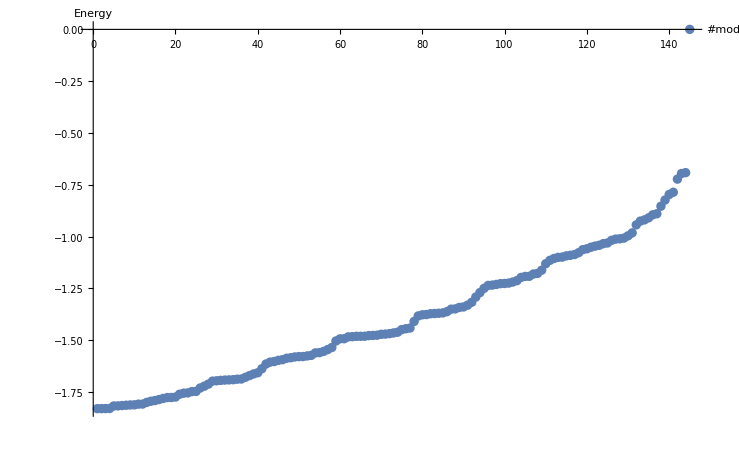

```mathematica
ListPlot[negEval~Join~zmEval,AxesLabel->{"#mode","Energy"}]
```

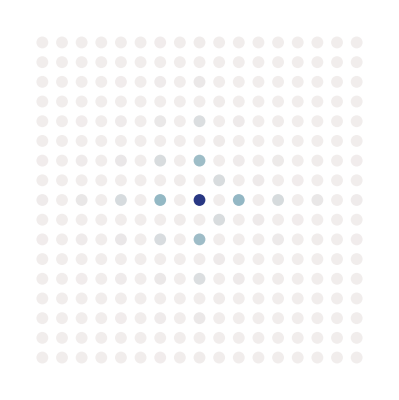

```mathematica
positions=positionList[graphCB];
max=Max[Sqrt@Total[zmEvec^2]];
zmPlot=Graphics[MapThread[{balanceBlueColorMap[Abs[#1]],Disk[#2,0.15]}&,{chiralList2[graphCB]Sqrt@Total[zmEvec^2],positions}]]
```

```mathematica
graphCB/.(Opacity[x__]:>Opacity[0.1])
```

-Graphics-

```mathematica
Show[graphCB,zmPlot]
```

-Graphics-

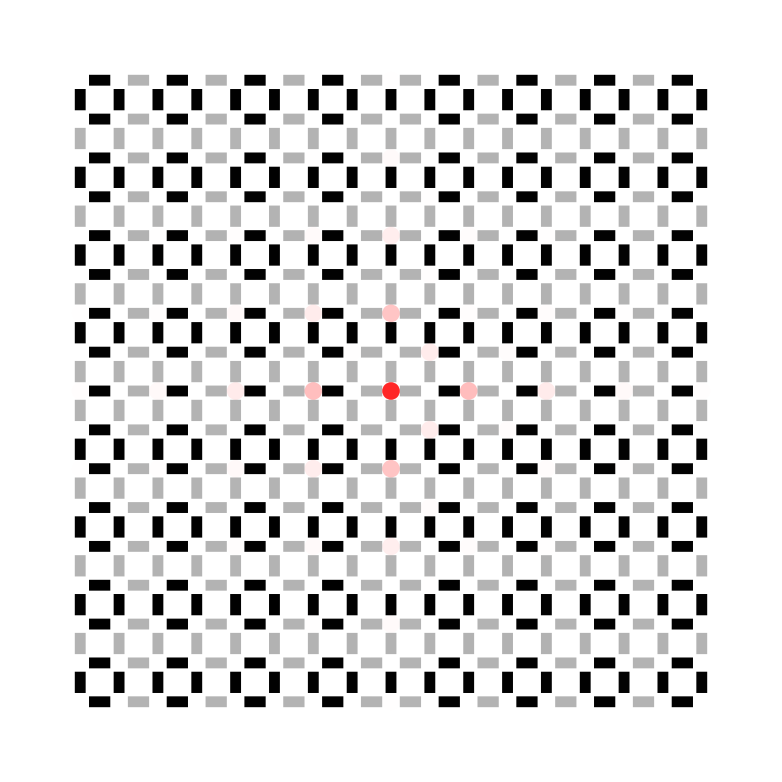

```mathematica
(*zero modes*)
highlightGraph[graphCB,Sqrt@Total[zmEvec^2],0.]
```

```mathematica
chiralPol=chiralPolarizationField[graphCB,basis];
plotChiralPolarizaionField[chiralPol,0.05][[1]]
Show[graphCB,Graphics[{Opacity[0.9],White,Rectangle[{0,0},{10,10}]}],plotChiralPolarizaionField[chiralPol,0.05][[1]]]
```

## Local perturbation

### Chiral Hamiltonian

```mathematica
h=WeightedAdjacencyMatrix[graphCB];
```

### Evolution of a perturbation localized in one node

```mathematica
c=chiralList2[graphCB];
pA=#>0&/@((ConstantArray[1,Length@c]+c)/2);
pB=(ConstantArray[1,Length@c]-c)/2;
pAn=Boole@pA;
pBn=pB;
positions=positionList[graphCB];
```

#### IC

```mathematica
rulesOneNodePerturbation=#->1.&/@Pick[VertexList@graphCB,pA];
initialStateOneNodePerturbation=With[{s1=VertexList[graphCB]},
(s1/.#/.x_Symbol[_,_]:>0)&/@rulesOneNodePerturbation
];
```

```mathematica
ax=1;
n=43;
img=Graphics[{MapThread[{balanceRedColorMap[Abs@#2],Disk[#1,ax/10]}&,{positions,pAn Abs@(initialStateOneNodePerturbation[[n]])}][[Flatten[Position[pAn,1]]]],MapThread[{balanceBlueColorMap[Abs@#2],Disk[#1,ax/10]}&,{positions,pBn Abs@(initialStateOneNodePerturbation[[n]])}][[Flatten[Position[pBn,1]]]]}];
```

```mathematica
indicesPerturbations={105,106,107,108,122,123,124,125};Show[graphCB,Graphics[Disk[positions[[Position[#,1.][[1,1]]]],0.3]&/@initialStateOneNodePerturbation[[indicesPerturbations]]]]
```

-Graphics-

```mathematica
Show[graphCB,Graphics[MapThread[{#1,Disk[positions[[Position[#2,1.][[1,1]]]],0.3]}&,{colorNodes,initialStateOneNodePerturbation[[indicesPerturbations]]}]]]
```

-Graphics-

#### Evolution

```mathematica
(*This line is only in case we want to add noise.
It significantly slows down the equation solver.*)
nSamples=30;
noise=Through[Table[Interpolation[{N@Range[0,tf,tf/(nSamples-1)],RandomReal[{0,0.02},nSamples]}ᵀ],Length@c][#]]&;
```

```mathematica
tf=10;
solsOneNodePerturbation=NDSolve[{ⅈ x'[t]==-(h).x[t],x[0]==#},x,{t,0,tf}]&/@initialStateOneNodePerturbation;
```

```mathematica
dt=0.1;
solTableOneNodePerturbation=Table[x[#]/.(sol[[1]])&/@Range[0,tf,dt],{sol,solsOneNodePerturbation}];
```

```mathematica
positions=positionList[graphCB];
momentsList=Quiet@Map[Map[With[{norm2=#*.#},
{
Sqrt[norm2],
(#*.(c#))/norm2,
1/norm2#*.((positions[[All,1]])#),
1/norm2#*.((positions[[All,2]])#),
1/norm2#*.(c(positions[[All,1]])#),
1/norm2#*.(c(positions[[All,2]])#)
}]&,#]&,solTableOneNodePerturbation];
```

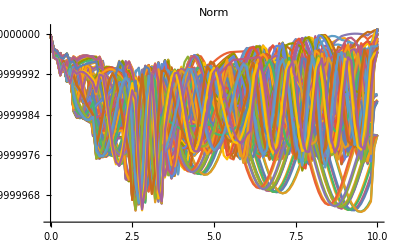
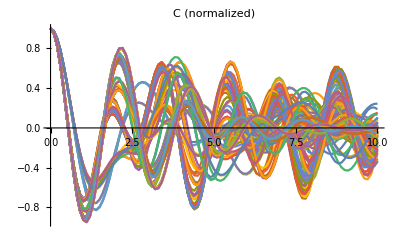
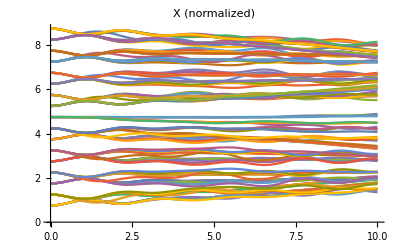
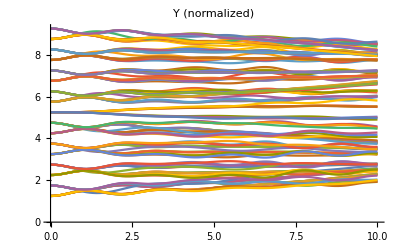
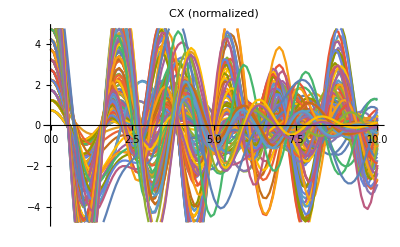
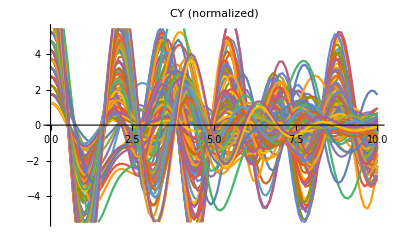

```mathematica
labelPlots={"Norm","C (normalized)", "X (normalized)", "Y (normalized)", "CX (normalized)", "CY (normalized)"};
axesl={"t (ms)",None};
ListPlot[{dt Range[0,Length[#]-1],#}ᵀ&/@(momentsList[[All,All,#]]),PlotLabel->labelPlots[[#]],FrameLabel->axesl,Joined->True]&/@Range[6]
```

#### Skip initial state to avoid complexinfinity in the mahalanobis distance

```mathematica
momentsList=momentsList[[All,2;;]];
```

#### Mahalanobis distance

```mathematica
weightsInTime=Map[Map[Chop[# #*]&,#]&,solTableOneNodePerturbation[[All,2;;]]]; (*we skip initial state*)
(*positions=positionsBeads~Join~positionsSprings;*)
weightedDataList=(WeightedData[positions,#]&/@#)&/@weightsInTime;
mahalanobisDistanceList=(With[{cov=Covariance[#],mean=Mean[#]},(√((#-mean).(Inverse[cov].(#-mean)))&/@positions)]&/@#)&/@weightedDataList;
```

#### Field time data

```mathematica
fieldTimeData=Chop@Map[{#[[3]],#[[4]],2(#[[5]]-#[[2]]#[[3]]),2(#[[6]]-#[[2]]#[[4]])}&,momentsList,{2}];
timeList=dt Range[0,Length[#1]-1]&/@fieldTimeData;
```

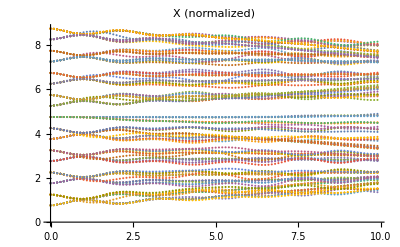
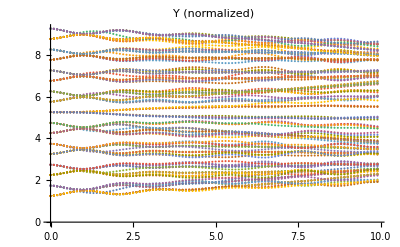
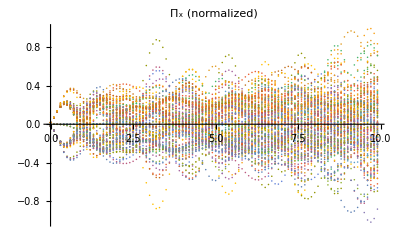
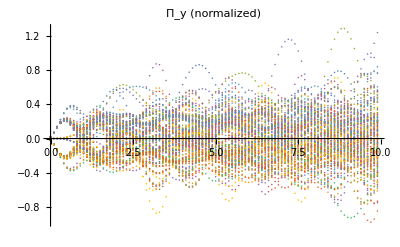

```mathematica
labelPlots={ "X (normalized)", "Y (normalized)", "Π_x (normalized)", "Π_y (normalized)"};
axesl={"t (ms)","(mm)"};
ListPlot[{dt Range[0,Length[#]-1],#}ᵀ&/@(fieldTimeData[[All,All,#]]),PlotLabel->labelPlots[[#]],FrameLabel->axesl]&/@Range[4]
```

```mathematica
distanceThreshold=1.8;
pickConfidenceList=((#<distanceThreshold)&/@#&/@#)&/@mahalanobisDistanceList;
```

#### Molecules

```mathematica
polygons2Dcolorless=Table[MapThread[With[{pts=Pick[positions,#]},If[Length@pts>1,If[CollinearPoints@pts,Nothing,{Opacity[0.1],EdgeForm[],ConvexHullMesh[pts]}],Nothing]]
&,{pickConfidenceList[[i]],timeList[[i]]}],{i,1,Length@pickConfidenceList}];
```

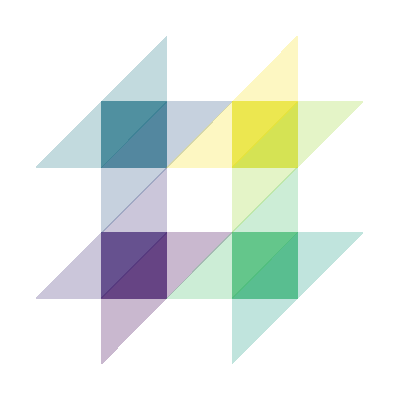

```mathematica
nData=10;
Graphics[MapThread[{#1,#2}&,{colorNodes,polygons2Dcolorless[[indicesPerturbations,;;nData]]}]]
```

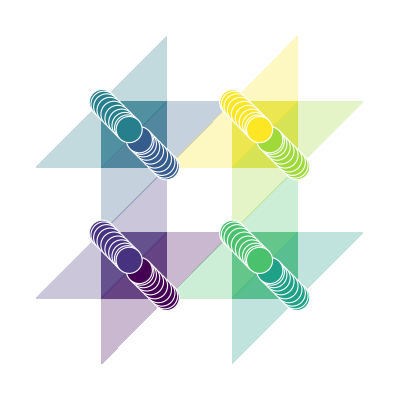

```mathematica
Show[Graphics[MapThread[{#1,#2}&,{colorNodes,polygons2Dcolorless[[indicesPerturbations,;;nData]]}]],Graphics[MapThread[{#1,EdgeForm[{Thickness[0.002],White}],Disk[#,0.1]&/@fieldTimeData[[#2,;;nData,{1,2}]]}&,{colorNodes,indicesPerturbations}]]]
```

```mathematica
atomA1Q[x_]:=If[Head[x]===$a1,True,False]
atomA2Q[x_]:=If[Head[x]===$a2,True,False]
maskAtomA1[graph_Graph]:=(2Boole@ atomA1Q[#]-1 )& /@ VertexList[graph];
maskAtomA2[graph_Graph]:=(2Boole@ atomA2Q[#]-1 )& /@ VertexList[graph];
```

```mathematica
auxindicesA1=Flatten[Position[maskAtomA1[graphCB],1]];
auxindicesA2=Flatten[Position[maskAtomA2[graphCB],1]];
indicesA1=Position[Sort[auxindicesA1~Join~auxindicesA2],#][[1,1]]&/@auxindicesA1;
indicesA2=Position[Sort[auxindicesA1~Join~auxindicesA2],#][[1,1]]&/@auxindicesA2;
```

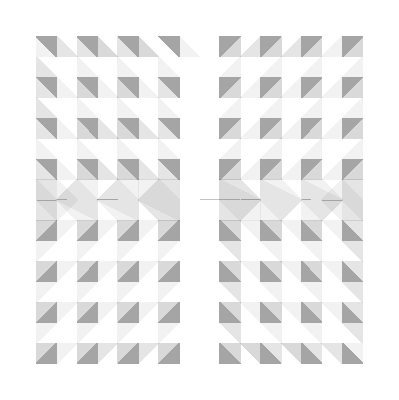

```mathematica
Graphics[polygons2Dcolorless[[indicesA1,;;8]]]
```

```mathematica
colorNodes
```

{RGBColor[0.267004, 0.004874, 0.329415],RGBColor[0.2747354285714286, 0.196969, 0.49725042857142854],RGBColor[0.21266685714285713, 0.35910242857142854, 0.5516348571428572],RGBColor[0.15295085714285714, 0.49805285714285713, 0.5576848571428572],RGBColor[0.12204571428571429, 0.632107, 0.530848],RGBColor[0.2900007142857143, 0.7588464285714286, 0.4278255714285714],RGBColor[0.6221707142857142, 0.8538152857142858, 0.226224],RGBColor[0.993248, 0.906157, 0.143936]}

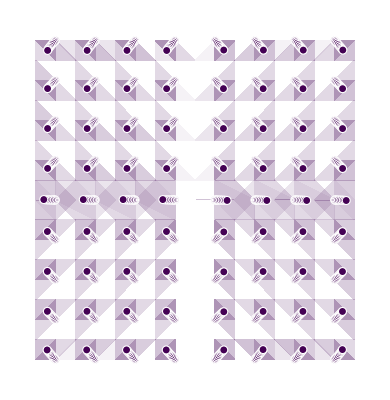
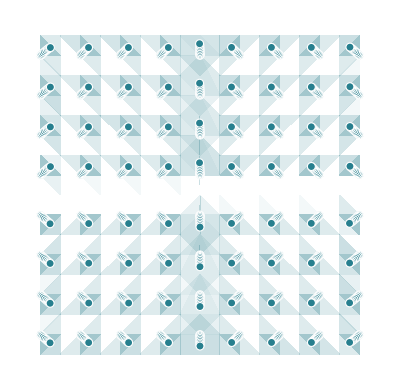

```mathematica
colorMolecules=colorNodes[[{1,4}]];
moleculesGraphics=MapThread[Show[Graphics[{#2,polygons2Dcolorless[[#1,;;nData]]}],Graphics[{#2,EdgeForm[{Thickness[0.002],White}],Disk[#,0.1]&/@Flatten[fieldTimeData[[#1,;;nData,{1,2}]],1]}]]&,{{indicesA1,indicesA2},colorMolecules}]
```

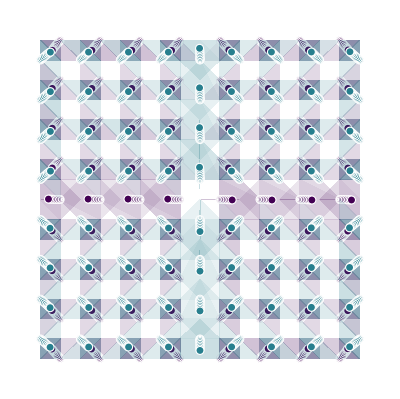

```mathematica
Show[moleculesGraphics]
```

#### Specific data for the article

We specify the colors from veridis and 8 perturbations

```mathematica
githubTextToList[text_String]:=ToExpression[StringReplace[text,{"["->"{","]"->"}"}]];
listViridis=;
viridisCM=Blend[RGBColor[#]&/@listViridis,#]&;
colorNodes=With[{n=8},viridisCM[(#-1)/(n-1)]&/@Range[n]];
```

```mathematica
With[{n=8},BarLegend[{viridisCM[(#-1)/(n-1)]&,{1,n}},n-1,AxesLabel->None]]
```

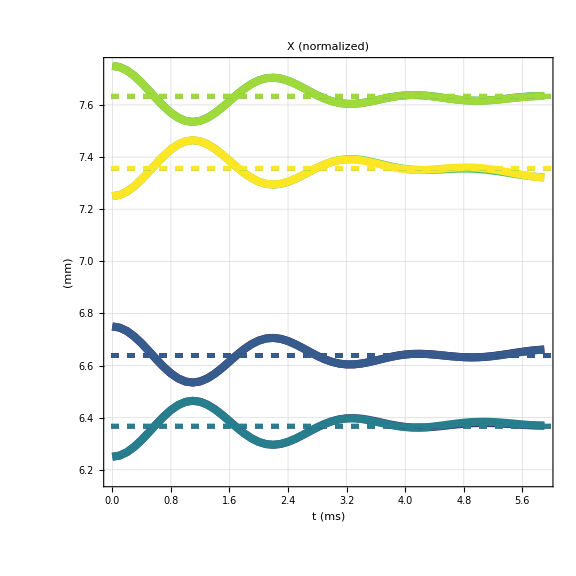
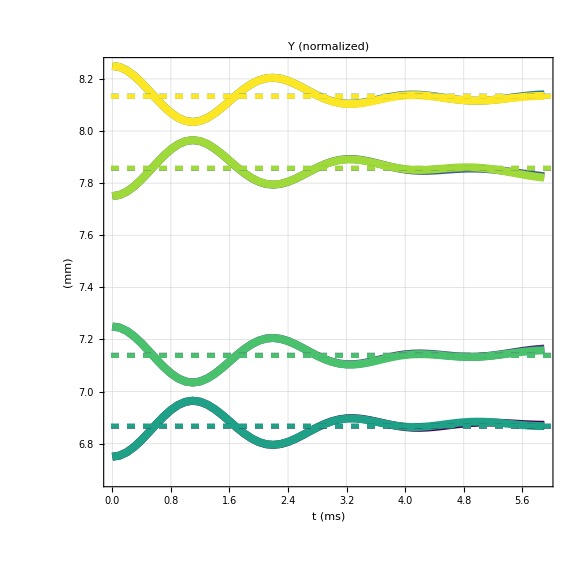
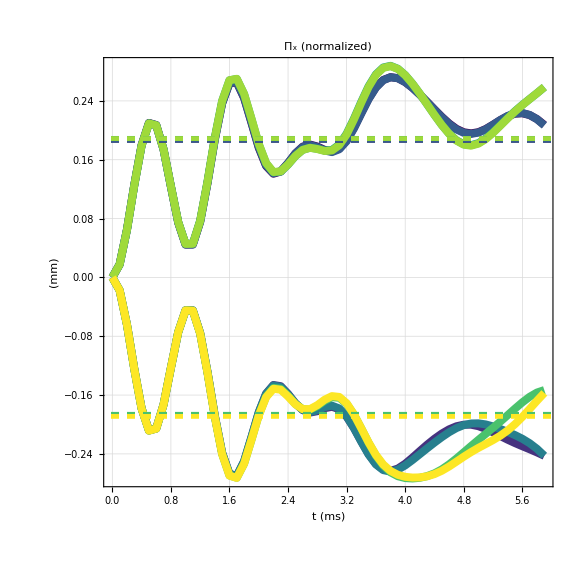
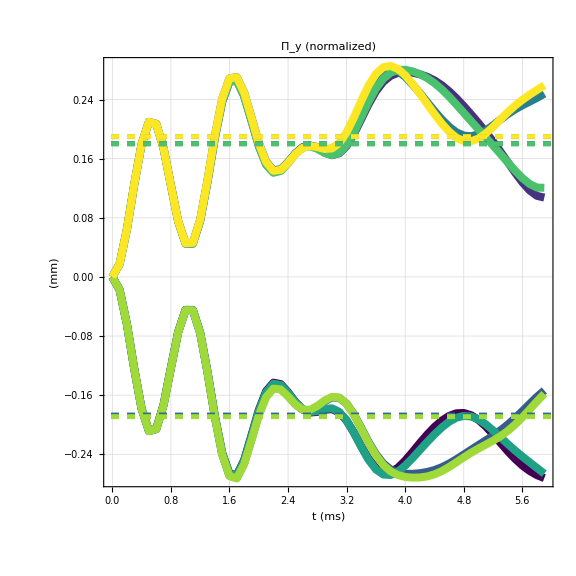

```mathematica
labelPlots={ "X (normalized)", "Y (normalized)", "Π_x (normalized)", "Π_y (normalized)"};
axesl={"t (ms)","(mm)"};
ListPlot[{dt Range[0,Length[#]-1],#}ᵀ&/@(fieldTimeData[[indicesPerturbations,;;3nData,#]]),PlotLabel->labelPlots[[#]],Frame->True,FrameLabel->axesl,Joined->True,ImageSize->Large,AspectRatio->1,GridLines->Automatic,FrameStyle->Directive[Black,FontSize->30],GridLinesStyle->Thickness[0.002],PlotStyle->({Thickness[0.01],#}&/@colorNodes),
Epilog->MapThread[{#1,Dashing[0.01],Thickness[0.006],InfiniteLine[{{0,Mean[#2]},{10,Mean[#2]}}]}&,{colorNodes,fieldTimeData[[indicesPerturbations,;;3nData,#]]}]
]&/@Range[4]
```

#### Evolution of centers

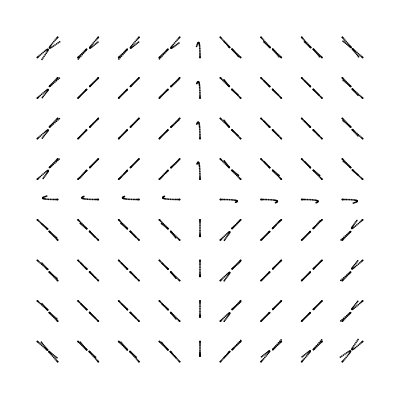

```mathematica
nData=20;
centers=Chop@Flatten[fieldTimeData[[All,1;;nData,{1,2}]],1];
Graphics[Disk[#,0.02]&/@centers]
```

#### Time averages

```mathematica
increasingAverageList[l_List]:=Module[{previous,current},previous=0;Table[current=(previous (i-1)+l[[i]])/i;previous=current;current,{i,1,Length@l}]]
```

```mathematica
iFrame=10;
timeAverageDataList=increasingAverageList[#]&/@(fieldTimeData[[All,iFrame;;,#]])&/@Range[4];
```

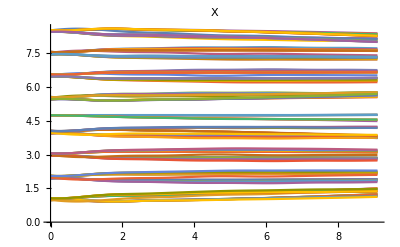
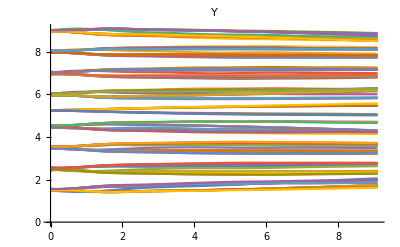
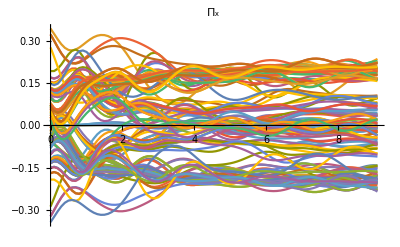
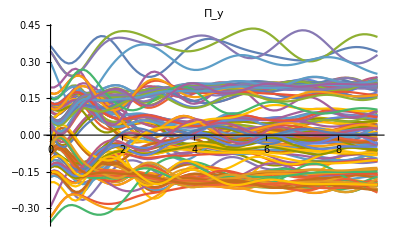

```mathematica
labelPlots={"X","Y","Π_x","Π_y"};
axesl={"Δ_t(ms)","mm"};
ListPlot[{dt Range[0,Length[#]-1],#}ᵀ&/@(timeAverageDataList[[#]]),FrameLabel->axesl,PlotLabel->labelPlots[[#]],Joined->True,PlotRange->All]&/@Range[4]
```

```mathematica
timeAverageDataList//Dimensions
```

{4,144,92}

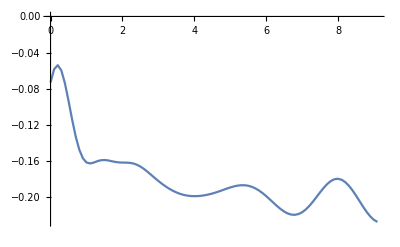

```mathematica
ListPlot[{dt Range[0,Length[#]-1],#}ᵀ&@(timeAverageDataList[[4,30]]),FrameLabel->axesl,Joined->True,PlotRange->All]
```

```mathematica
nFramesAverage=nData;
meanAroundDataList=MeanAround[#]&/@(fieldTimeData[[All,iFrame;;iFrame+nFramesAverage-1,#]])&/@Range[4];
meanDataList=Mean[#]&/@(fieldTimeData[[All,iFrame;;iFrame+nFramesAverage-1,#]])&/@Range[4];
stdDataList=StandardDeviation[#]&/@(fieldTimeData[[All,iFrame;;iFrame+nFramesAverage-1,#]])&/@Range[4];
(*Attenstion: this is the angle of the means*)
meanAroundAngleList=ArcTan@@#&/@(meanAroundDataList[[3;;4]]ᵀ);
```

```mathematica
meanAngleList=ArcTan@@#&/@(meanDataList[[{3,4}]]ᵀ);
dfdx[x_,y_]=D[ArcTan[x,y], x];
dfdy[x_,y_]=D[ArcTan[x,y], y];
stdAngleList=MapThread[Sqrt[((dfdx@@#1)#2[[1]])^2+((dfdy@@#1)#2[[2]])^2]&,{meanDataList[[{3,4}]]ᵀ,stdDataList[[{3,4}]]ᵀ}];
```

```mathematica
refImage=Show[img,Graphics[{Blue,Disk[#,3]&/@(timeAverageDataList[[{1,2},All,nFramesAverage]]ᵀ)}]];
```

### Graphics

```mathematica
fcolor=GrayLevel[(35-#)/35]&;
barl=BarLegend[{fcolor[#]&,{0,40}},LegendLabel->"Norm",LabelStyle->Directive[Black,FontSize->14]];
primitivesList=MapThread[Module[{center={#1[[1]],#1[[2]]},pol={#1[[3]],#1[[4]]},unitvector,norm,circleRadius=15},
norm=Norm@pol;
unitvector=Normalize[pol];
{fcolor[norm],Thickness[0.005],Arrowheads[.04],Arrow[{center-unitvector circleRadius,center+unitvector circleRadius}],Thickness[0.002],Circle[center,circleRadius],Thickness[0.008],Circle[center,circleRadius,{#2-#3,#2+#3}]}
]&,{meanDataListᵀ,meanAngleList,stdAngleList}];
primitivesList2=MapThread[Module[{center={#1[[1]],#1[[2]]},pol={#1[[3]],#1[[4]]},unitvector,norm,circleRadius=15},
norm=Norm@pol;
unitvector=Normalize[pol];
{Opacity[0.6],RGBColor[#/255&/@{244,212,139}],Disk[center,circleRadius],Opacity[1],fcolor[norm],Thickness[0.005],Arrowheads[.04],Arrow[{center-unitvector circleRadius,center+unitvector circleRadius}],Thickness[0.008],Circle[center,circleRadius,{#2-#3,#2+#3}]}
]&,{meanDataListᵀ,meanAngleList,stdAngleList}];
```

```mathematica
customColorF = Blend[{RGBColor[0.685695, 0.242449, 0.268261], RGBColor[
    0.534081, 0.0853132, 0.16669], GrayLevel[0], RGBColor[
    0.139681, 0.311666, 0.550652], RGBColor[
    0.256859, 0.523007, 0.711644], RGBColor[
    0.433786, 0.670834, 0.793785], RGBColor[0.289326, 0.685107, 0.24], 
    RGBColor[0., 0.442859, 0.0749256], RGBColor[
    0.44, 0.685107, 0.108759], RGBColor[0.87, 0.67, 0.522424], 
    RGBColor[0.685695, 0.242449, 0.268261]}, #] &;
colorDisk = 
        With[ {offset = -1.5, sectors = 360., angleAux = 2. Pi/360},
            Graphics[
             Table[{customColorF[i/sectors], 
               EdgeForm[{Thick, customColorF[i/sectors]}], 
               Annulus[{0, 0}, {1/2, 
                 1}, {i angleAux + offset, (i + 1) angleAux + offset}]}, {i, 0,
                sectors - 1}], ImageSize -> Tiny]
        ];
```

```mathematica
primitivesList3=MapThread[Module[{center={#1[[1]],#1[[2]]},pol={#1[[3]],#1[[4]]},unitvector,norm},
norm=Norm@pol;
unitvector=Normalize[pol];
{customColorF[Mod[1 + #2/(2 π) + 0.2, 1]],Arrowheads[.02],Thickness[0.007],Arrow[{center-pol/2,center+pol/2}]}
]&,{meanDataListᵀ,meanAngleList,stdAngleList}];
```

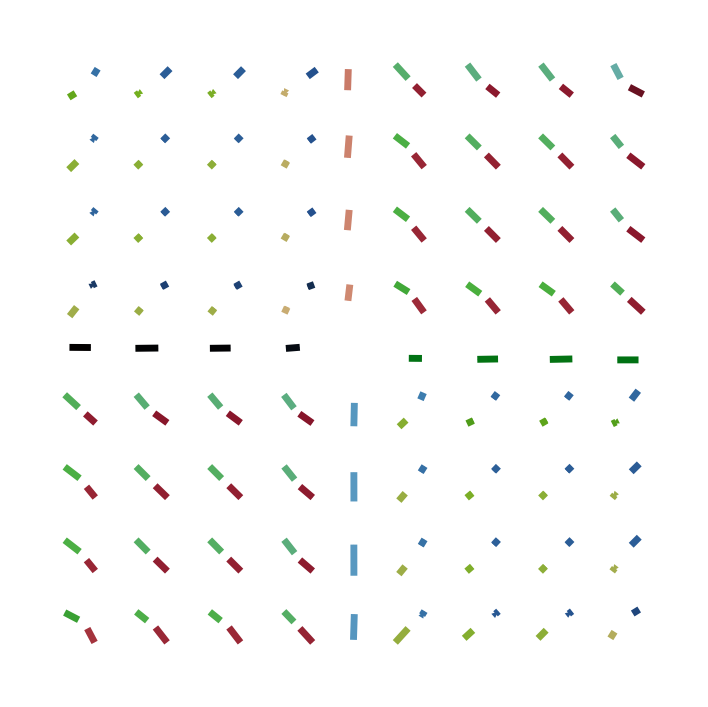

```mathematica
Graphics[primitivesList3]
```

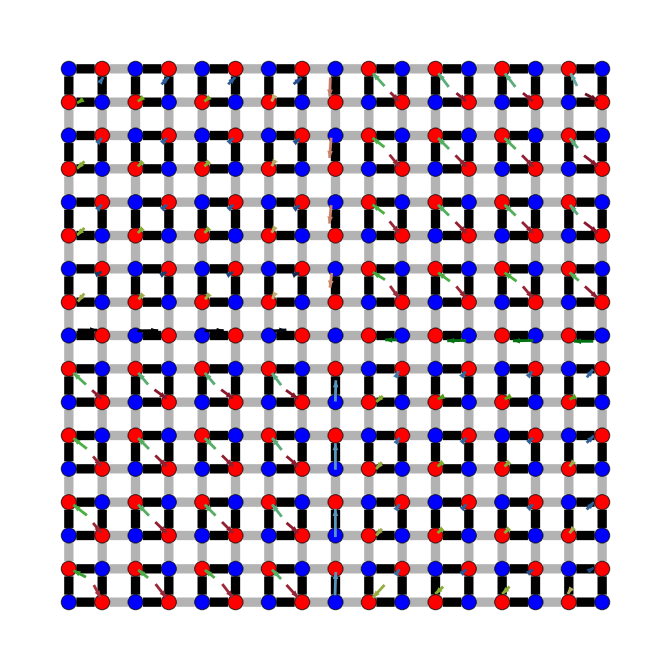

```mathematica
Show[graphCB,Graphics[primitivesList3]]
```

```mathematica
averageData={meanDataList[[{1,2}]]ᵀ,meanDataList[[{3,4}]]ᵀ}ᵀ;
```

```mathematica
(*group by distance*)
groupByDistance=Gather[averageData,Norm[#1[[1]]-#2[[1]]]<0.5&];
(*remove singlets*)
groupByDistance=Select[groupByDistance,Length@#>=1&];
```

```mathematica
moleculeCentersAndPols=Mean[#]&/@groupByDistance;
```

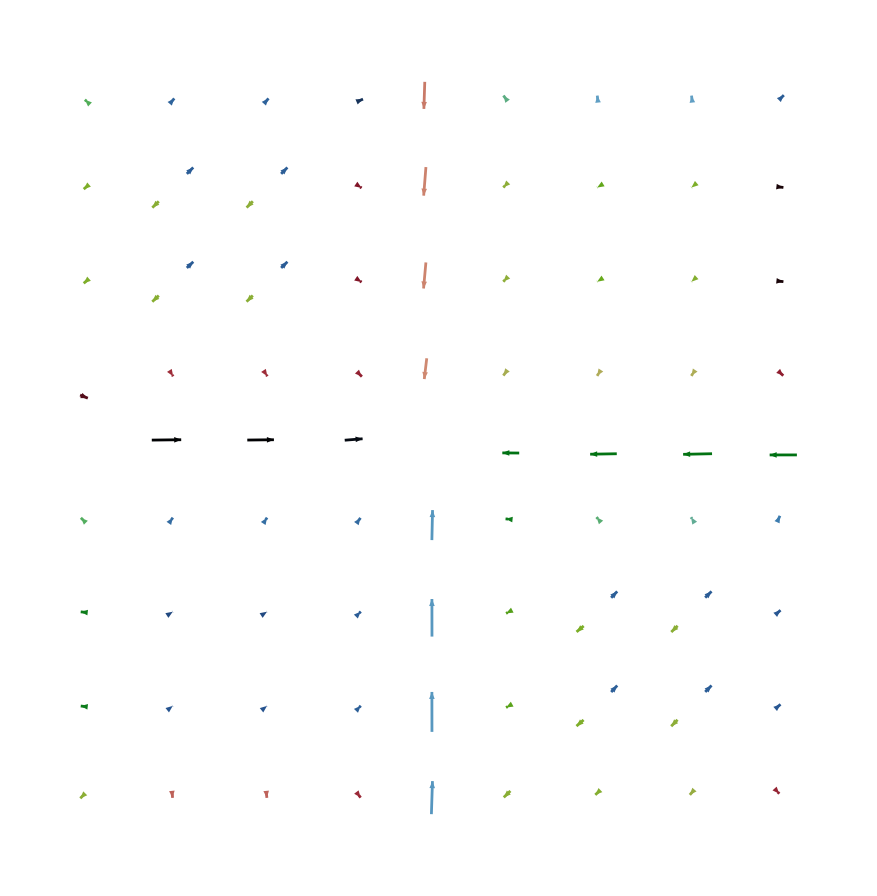

```mathematica
plotChiralPolarizaionField[moleculeCentersAndPols[[All,1]]ᵀ~Join~(moleculeCentersAndPols[[All,2]]ᵀ),0.06][[1]]
```

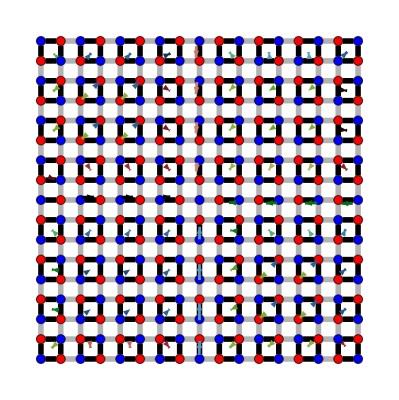

```mathematica
Show[graphCB,-Graphics-]
```

## Utils

```mathematica
SetDirectory[NotebookDirectory[]];
```

#### createGraphCheckerboard

```mathematica
{$bravais1,$bravais2}={{1,0},{0,1}};

edgeStyle[edges_List,edgeWeights_List,factor_:1]:=With[{max=Max@edgeWeights,opacityWeight=Directive[Black,Opacity[Abs[#]]]&},MapThread[#1->opacityWeight[#2/(factor max)]&,{edges,edgeWeights}]]
edgeStyle[___]:=(Message[edgeStyle::badarg];
$Failed)

pChargeQ[x_]:=If[Head[x]===$a1||Head[x]===$a2,True,False]
mChargeQ[x_]:=If[Head[x]===$b1||Head[x]===$b2,True,False]

chiralList2[graph_Graph]:=(2Boole@ pChargeQ[#]-1 )& /@ VertexList[graph];

createGraphCheckerboard[nCellsx_Integer,nCellsy_Integer,interactions1_List,atomicPositions_List,dSpositions_:0,dSinteractions_:0,sigmaInteractions_:15]:=Module[{graph,vertex,edges,edgeWeights,positions},$nCellsx=nCellsx;
$nCellsy=nCellsy;
$dSinteractions=dSinteractions;
$dSpositions=dSpositions;
{$rA1,$rB1,$rA2,$rB2}=atomicPositions;
vertex=With[{vertexUC={$a1[#1,#2],$b1[#1,#2],$a2[#1,#2],$b2[#1,#2]}&},Flatten[Table[vertexUC[i,j],{i,nCellsx},{j,nCellsy}],2]];
positions=With[{positionsUC=ConstantArray[(#1-1) $bravais1+(#2-1) $bravais2,{4}]+{$rA1,$rB1,$rA2,$rB2}+#3 RandomReal[{-1,1},{4,2}]&},Flatten[Table[positionsUC[i,j,dSpositions],{i,nCellsx},{j,nCellsy}],2]];
$randomFields[{x_,y_}]=Module[{nGaussians,acoefs,std,pos,regionSystem},regionSystem=Polygon[{{0,0},$bravais1*nCellsx,$bravais1*nCellsx+$bravais2*nCellsy,$bravais2*nCellsy}];
nGaussians=Floor@N[Area[regionSystem]/sigmaInteractions^2];
acoefs=Partition[RandomVariate[NormalDistribution[0,dSinteractions],8 nGaussians],nGaussians] (ConstantArray[{1,1,1,1,1,1,1,1},nGaussians]ᵀ);
pos=RandomPoint[regionSystem,nGaussians];
std=N@Sqrt[π nGaussians/Area[regionSystem]] dSinteractions sigmaInteractions;
(*corrLength=2 sigma;*)Total[MapThread[#1 E^(-({x,y}-#2).({x,y}-#2)/(2 sigmaInteractions^2))&,{#,pos}]]&/@acoefs];
{edges,edgeWeights}=With[{edgesUC={$a1[#1,#2]<->$b1[#1,#2],$a1[#1,#2]<->$b2[#1,#2],$a2[#1,#2]<->$b1[#1,#2],$a2[#1,#2]<->$b2[#1,#2],$a1[#1+1,#2]<->$b1[#1,#2],$a2[#1,#2]<->$b2[#1+1,#2],$a2[#1,#2]<->$b1[#1,#2+1],$a1[#1,#2+1]<->$b2[#1,#2]}&,edgeWeightsUC=interactions1+(#3[#1 $bravais1+#2 $bravais2])&},Flatten[Table[#,{i,nCellsx},{j,nCellsy}],2]&/@{edgesUC[i,j],edgeWeightsUC[i,j,$randomFields]}];
{edges,edgeWeights}={EdgeList[#],PropertyValue[#,EdgeWeight]}&@(Subgraph[Graph[edges,EdgeWeight->edgeWeights],vertex]);
(*Graph*)graph=Graph[Graph[vertex,edges,VertexStyle->{_?pChargeQ->Directive[RGBColor[{179,56,38}/255],EdgeForm[None]],_?mChargeQ->Directive[RGBColor[{22,112,188}/255],EdgeForm[None]]},VertexCoordinates->positions,EdgeWeight->edgeWeights,EdgeStyle->edgeStyle[edges,edgeWeights]],EdgeStyle->Thickness[0.01],VertexSize->{"Scaled",0.02}];
AnnotationValue[graph,"Size UC"]={nCellsx,nCellsy};
AnnotationValue[graph,"position disorder"]=dSpositions;
AnnotationValue[graph,"interaction disorder"]=dSinteractions;
graph]
createGraphCheckerboard[___]:=(Message[createGraphCheckerboard::badarg];
$Failed);
```

```mathematica
githubTextToList[text_String]:=ToExpression[StringReplace[text,{"["->"{","]"->"}"}]];
listBlue=ToExpression@;
listRed=ToExpression@;

(*Color map functions*)
balanceRedColorMap=Blend[Reverse[RGBColor[#]&/@listRed],#]&;
balanceBlueColorMap=Blend[Reverse[RGBColor[#]&/@listBlue],#]&;
```